------------------------2/16-----------------------

0.301438

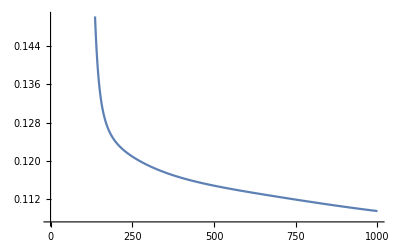

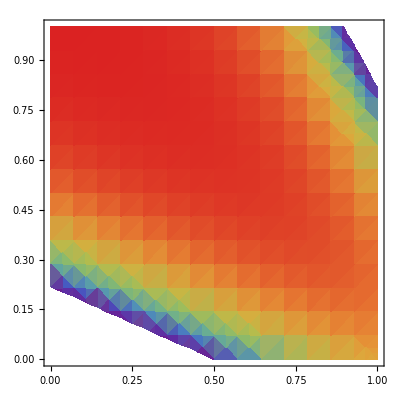

------------------------4/16-----------------------

0.244366

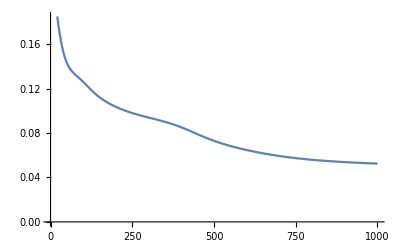

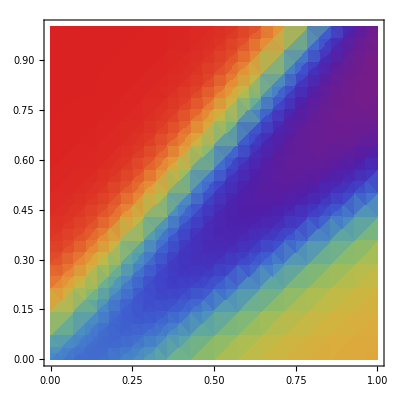

------------------------8/16-----------------------

0.239829

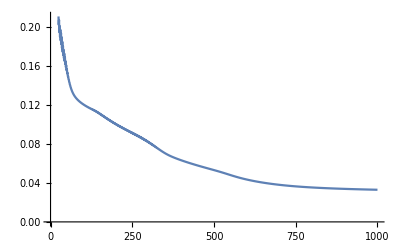

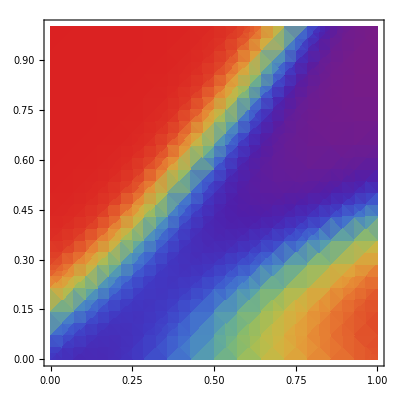

------------------------2/32-----------------------

0.274974

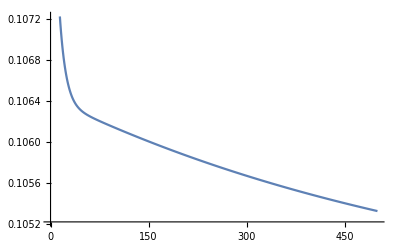

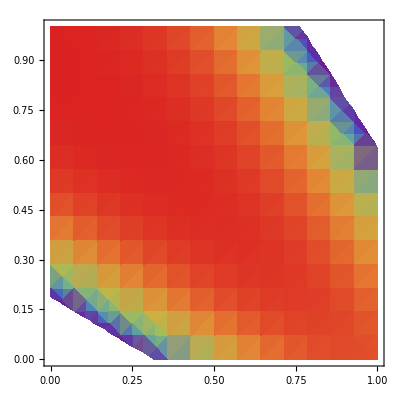

------------------------4/32-----------------------

0.302535

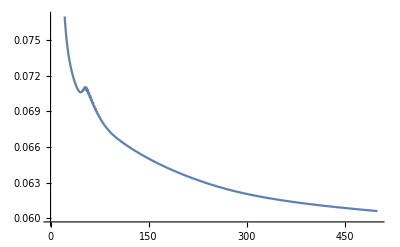

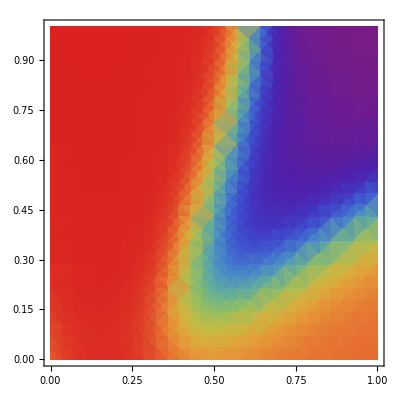

------------------------8/32-----------------------

0.276315

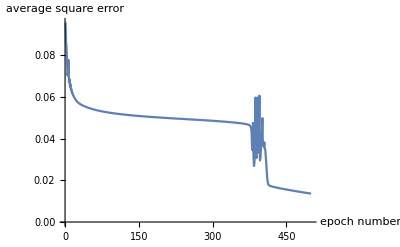

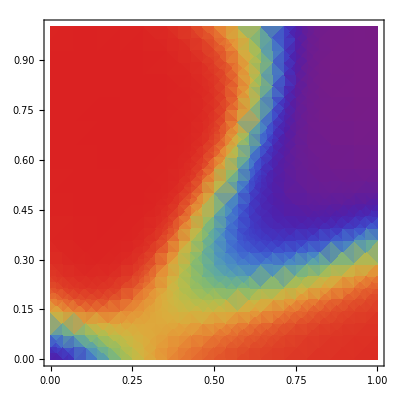

------------------------2/64-----------------------

0.234765

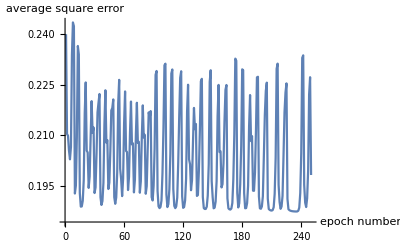

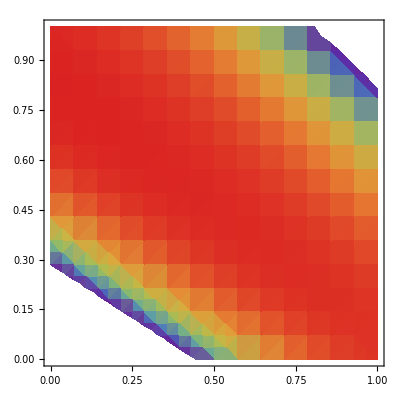

------------------------4/64-----------------------

0.249841

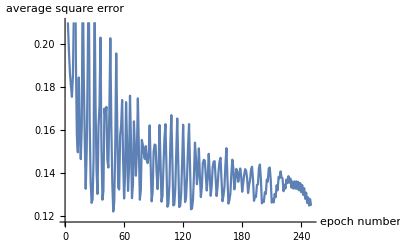

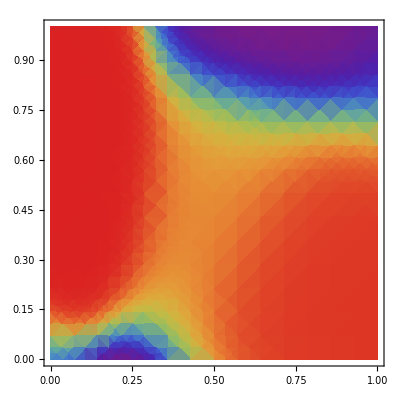

------------------------8/64-----------------------

0.274166

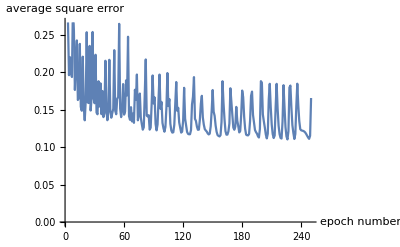

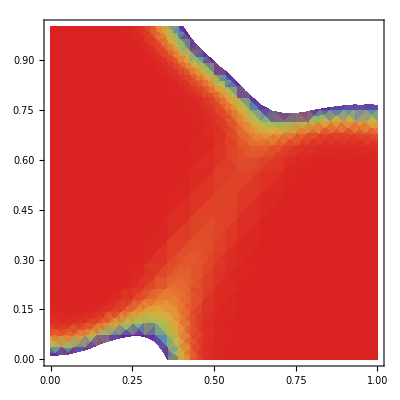

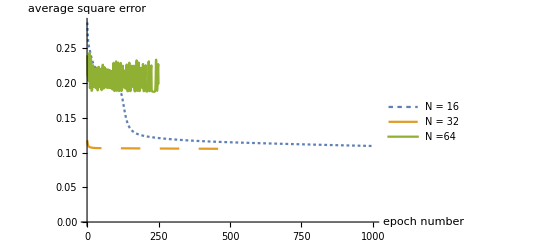

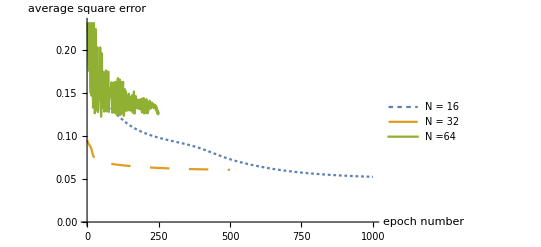

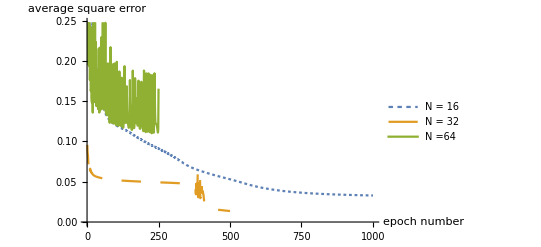

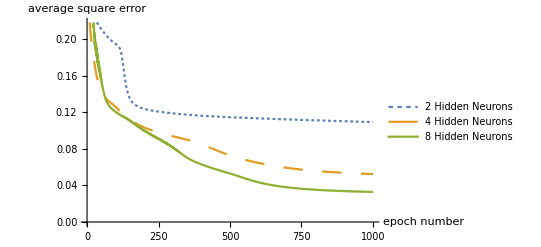

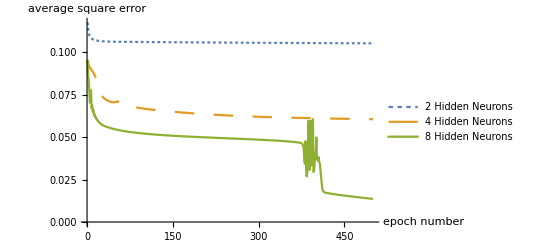

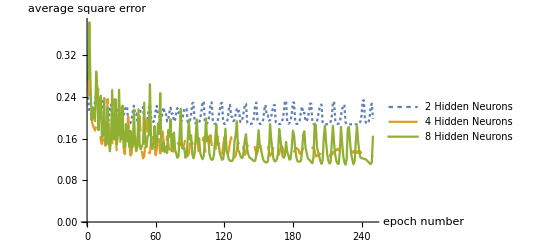

```mathematica
(* ::Package::*)

(*Mathematica Code for MLP*)
(*Normal random variables with variance 1*)
xrv:=2{Random[],Random[]}-1;
gauss:=Module[{t},t=xrv;t=If[t.t≥1,gauss,t[[1]]Sqrt[-2Log[t.t]/t.t]]];
noise1=Table[.5{gauss,gauss},{i,1000}];(*Normal noise var=0.25*)
noise2=Table[.5{gauss,gauss},{i,1000}];(*Normal noise var=0.25*)

trainSize=64;
hiddenNeurons=8;
iterations=1000;
(*Logistic function:*)
f[x_]=1/(1+Exp[-x]);(*works on vectors component-wise*)



weight1TwoHidden={{-1.1584917264152108,0.8851638269350084,-0.437090407518425},{-0.3787556600698261,0.48991306808406465,1.0532859918231807}};
weight2TwoHidden={-1.6580779583970404,-1.2103699644244454,-1.0814717551591504};
weight1FourHidden={{-1.1584917264152108,0.8851638269350084,-0.437090407518425},{-0.3787556600698261,0.48991306808406465,1.0532859918231807},{0.6906774909754727,-1.2562396803966913,0.6055224991776322},{-1.0453655321496325,-1.3598638998608554,0.4931203579753838}};
weight2FourHidden={-1.6580779583970404,-1.2103699644244454,-1.0814717551591504,-1.9693993279724473,-0.1479910264811053};
weight1EightHidden={{-1.1584917264152108,0.8851638269350084,-0.437090407518425},{-0.3787556600698261,0.48991306808406465,1.0532859918231807},{0.6906774909754727,-1.2562396803966913,0.6055224991776322},{-1.0453655321496325,-1.3598638998608554,0.4931203579753838},{-1.732356067166775,-0.6110804964565404,0.14486753509692818},{-1.562135975007601,-1.8109980467573292,-0.792770320873474},{1.7607046180590156,-1.91335013095563,-0.8165696848122512},{1.6747938625105627,0.4814378373224244,-0.3481549880422734}};
weight2EightHidden={-1.6580779583970404,-1.2103699644244454,-1.0814717551591504,-1.9693993279724473,-0.1479910264811053,-0.26365595624762617,0.2278507538653769,1.2868403524242442,1.2464864743412627};


testset={{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1}};
testout=Abs[{1,-1}.testset];
testset=Join[testset+Transpose[Take[noise2,64]],{Take[ones,64]}];

etab16=Table[0,{iterations}];
etab2H16=Table[0,{iterations}];
etab4H16=Table[0,{iterations}];
sampleetab16=Table[0,{iterations/10}];

etab32=Table[0,{iterations/2}];
etab4H32=Table[0,{iterations/2}];
etab2H32=Table[0,{iterations/2}];
sampleetab32=Table[0,{iterations/20}];

etab64=Table[0,{iterations/4}];
etab2H64=Table[0,{iterations/4}];
etab4H64=Table[0,{iterations/4}];
sampleetab64=Table[0,{iterations/40}];
(*and an offset vector:*)
ones=Table[-1,{64}];
train16={{-0.28552913795916557,0.7195684647840876,0.6428144957304299,-1.2214079369733455,0.12156358903633763,-0.02681021984035775,0.5253360707042003,0.023017785419832435,1.3647068066067805,0.6169169398171841,-0.05097468069223843,0.9621930482182198,2.0039712581490337,1.494941053721349,1.8232834908098776,1.3095628634378593},{-0.1351850177267172,-0.6461033522630971,0.3936361253161326,-0.4818122191520221,0.8531248252818876,0.4283287710031124,0.9239675446441595,2.3408069389964883,0.12617277126971443,-0.7840018877126417,0.28585540924776964,0.20172296638013348,0.9227672145623982,1.9034208974172464,1.0814599466665706,0.7678062251139949},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}};
train16out={0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0};

train32={{-0.28552913795916557,0.7195684647840876,0.6428144957304299,-1.2214079369733455,0.12156358903633763,-0.02681021984035775,0.5253360707042003,0.023017785419832435,1.3647068066067805,0.6169169398171841,-0.05097468069223843,0.9621930482182198,2.0039712581490337,1.494941053721349,1.8232834908098776,1.3095628634378593,-1.0147966566702842,-0.9981210089769575,-0.24653774590506272,0.21248328797595567,0.9820948173375194,-0.2889487200360429,0.15223140224400994,-0.061342860161801786,0.8180663203622411,1.4070169662538414,1.396608609796169,0.19048752447837047,1.9050498379614096,0.6929348834662405,1.6402384757155777,1.5483652008732354},{-0.1351850177267172,-0.6461033522630971,0.3936361253161326,-0.4818122191520221,0.8531248252818876,0.4283287710031124,0.9239675446441595,2.3408069389964883,0.12617277126971443,-0.7840018877126417,0.28585540924776964,0.20172296638013348,0.9227672145623982,1.9034208974172464,1.0814599466665706,0.7678062251139949,-0.06267965699616611,-0.09738616455723009,1.258834235172041,-0.9181325633482432,-0.25687284722426185,0.8644818815061412,0.6687933835399065,1.952064396818376,-0.03615542602466572,-0.4558139510327045,0.19052069816031544,0.5088150890738556,0.6971404022059422,1.2709515185765843,0.9113841549840859,1.0686017159528414},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}};
train32out={0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0};

train64={{0.5433719981429767,-0.6731427164021281,0.37153185789053716,-1.058969581256266,0.6672108291376684,0.11137895783055274,-0.6635579713627339,-0.3493899511348217,0.845873280519235,-0.12118815371787672,0.3795521764112374,0.79539445567662,1.1887845753731365,0.35130148618472756,0.7460876379166634,1.4107462043004233,-0.5953328968869244,0.33644176835114586,-0.6547935950665994,-0.03874446810555093,-0.305501399532944,-0.6289568257795877,-0.056856151302898617,0.7150409694313724,1.3996496138433414,0.8601907066663869,0.9396325910129384,0.6675299369515415,0.6241585864477383,0.9905391956388255,0.5984006685371764,1.4590754949742124,0.7951045959030182,-0.6990109983424261,0.08979687105517459,-0.1365215284595569,-0.17890447357986236,1.4116704522947496,0.8778121321059575,-0.8770816809920003,0.4197267239049898,1.8117711819018791,1.100599758986621,0.39194862767602534,0.36579043561677294,1.0147613551109758,1.9602570265435388,1.274010982484577,1.1771652813566844,0.2866693496109699,-0.3570119345547125,0.4124353637600567,-0.07429880191779542,-0.5832609038976414,0.22158070171404576,-0.6253077508787888,1.2324122794778272,1.1143984424756783,1.459758025791613,0.5500891339828871,2.1543757254234777,0.591382203722159,1.9228457023015342,0.8246576287292029},{0.38146125195437797,0.543341008485442,0.3025605630175848,-0.16559617636346532,0.9872524603279234,0.8457465040463573,0.8948242754169144,2.214341699033864,0.4627749565415458,0.23436473124467003,0.42646052417658725,0.09434381745310697,1.3038131701554168,1.4145241474788188,0.8788862234426948,0.9265757308211917,0.19593395468737043,1.213769012876916,0.3684565059977865,-1.030859256187006,0.5191739142874872,0.8081090696860751,0.7311396622579358,0.6368236945704386,0.34661840927912574,0.3757281842145653,0.2710146886191859,-0.15407161327056496,0.7389273729581183,1.5121347418031108,0.8855052100817292,1.534201524091573,0.0076004851505857215,-0.9128527297137113,-1.0016124202945205,-0.1205198696934828,1.3936887142208818,1.0386522174252586,1.471947999646745,2.0676792085969744,0.5716178247606677,0.287023036295689,-0.48524851534478014,0.2670426595462622,1.1841190003570976,0.8354844992829809,1.5384644107103593,1.068335332889014,-0.5466431712526738,-0.03578862879266151,0.33974073453398423,0.06011233866857057,1.4928106110916075,0.3538344572599813,1.2818698707770761,0.8465984915027294,0.020535697210430526,-0.4119587814820964,0.09839570094047592,0.06692907167263022,1.5722282806437016,1.0524730148386152,0.5056129181995667,1.4716524601309817},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}};
train64out={0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0};

(*Target output*)
If[trainSize==16,trainop=train16out;train=train16wnoise;,0;]
If[trainSize==32,trainop=train32out;train=train32wnoise;,0;]
If[trainSize==64,trainop=train64out;train=train64wnoise;,0;]
(*{0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0};*)

(*Full set of training vectors*)

(*Training patterns are 3*16 matrix;last row is offset:*)
(*{{-0.310691,-0.309003,1.25774,1.31959,-0.0897083,-0.457115,1.42524,1.43962,-0.21377,-0.16744,0.579612,1.90558,0.442017,0 .204012,1.75664,0.584128},{0.0164278,0.898471,-0.231735,0.82952,-1.02045,1.84369,0.111823,0.28365,0.0759174,0.985518,0.584378,0.434351,0.35245,-0.0194183,-0.336488,1.45608},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}};*)
(*Then the training loop of 1000 epochs:*)
Print["------------------------2/16-----------------------"];
Do[hid=f[weight1TwoHidden.train16];(*hidden outputs*)out=f[weight2TwoHidden.Join[hid,{Take[ones,16]}]];(*net output*)e=train16out-out;(*output error*)etab16[[i]]=e.e/16;(*squared error on epoch i*)deltaout=e*out(1-out);(*delta for output unit*)ehid=Take[Outer[Times,weight2TwoHidden,deltaout],2];(*backpropagate,strip offset*)deltahid=ehid*hid*(1-hid);(*get delta for hidden layer*)weight2TwoHidden+=deltaout.Transpose[Join[hid,{Take[ones,16]}]];(*update output weight matrix*)weight1TwoHidden+=deltahid.Transpose[train16];(*hidden weight matrix*)If[Mod[i,10]==0,sampleetab16[[i/10]]=etab16[[i]],0]
(*If[Mod[i,100]==0,Print[etab16[[i]]],0]*),{i,iterations}]

hid=f[weight1TwoHidden.testset];(*hidden outputs*)out=f[weight2TwoHidden.Join[hid,{Take[ones,64]}]];(*net output*)error=testout-out;
error.error/64
ListLinePlot[etab16]
DensityPlot[f[weight2TwoHidden.Join[f[weight1TwoHidden.{{x},{y},{-1}}],{{-1}}]],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]
etab2H16=etab16;

Print["------------------------4/16-----------------------"];
Do[hid=f[weight1FourHidden.train16];(*hidden outputs*)out=f[weight2FourHidden.Join[hid,{Take[ones,16]}]];(*net output*)e=train16out-out;(*output error*)etab16[[i]]=e.e/16;(*squared error on epoch i*)deltaout=e*out(1-out);(*delta for output unit*)ehid=Take[Outer[Times,weight2FourHidden,deltaout],4];(*backpropagate,strip offset*)deltahid=ehid*hid*(1-hid);(*get delta for hidden layer*)weight2FourHidden+=deltaout.Transpose[Join[hid,{Take[ones,16]}]];(*update output weight matrix*)weight1FourHidden+=deltahid.Transpose[train16];(*hidden weight matrix*)If[Mod[i,10]==0,sampleetab16[[i/10]]=etab16[[i]],0]
(*If[Mod[i,100]==0,Print[etab16[[i]]],0]*),{i,iterations}]
hid=f[weight1FourHidden.testset];(*hidden outputs*)out=f[weight2FourHidden.Join[hid,{Take[ones,64]}]];(*net output*)error=testout-out;
error.error/64
ListLinePlot[etab16]
etab4H16=etab16;
DensityPlot[f[weight2FourHidden.Join[f[weight1FourHidden.{{x},{y},{-1}}],{{-1}}]],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]

Print["------------------------8/16-----------------------"];
Do[hid=f[weight1EightHidden.train16];(*hidden outputs*)out=f[weight2EightHidden.Join[hid,{Take[ones,16]}]];(*net output*)e=train16out-out;(*output error*)etab16[[i]]=e.e/16;(*squared error on epoch i*)deltaout=e*out(1-out);(*delta for output unit*)ehid=Take[Outer[Times,weight2EightHidden,deltaout],8];(*backpropagate,strip offset*)deltahid=ehid*hid*(1-hid);(*get delta for hidden layer*)weight2EightHidden+=deltaout.Transpose[Join[hid,{Take[ones,16]}]];(*update output weight matrix*)weight1EightHidden+=deltahid.Transpose[train16];(*hidden weight matrix*)If[Mod[i,10]==0,sampleetab16[[i/10]]=etab16[[i]],0]
(*If[Mod[i,100]==0,Print[etab16[[i]]],0]*),{i,iterations}]
hid=f[weight1EightHidden.testset];(*hidden outputs*)out=f[weight2EightHidden.Join[hid,{Take[ones,64]}]];(*net output*)error=testout-out;
error.error/64
ListLinePlot[etab16]
DensityPlot[f[weight2EightHidden.Join[f[weight1EightHidden.{{x},{y},{-1}}],{{-1}}]],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]

iterations=iterations/2;
Print["------------------------2/32-----------------------"];
Do[hid=f[weight1TwoHidden.train32];(*hidden outputs*)out=f[weight2TwoHidden.Join[hid,{Take[ones,32]}]];(*net output*)e=train32out-out;(*output error*)etab32[[i]]=e.e/32;(*squared error on epoch i*)deltaout=e*out*(1-out);(*delta for output unit*)ehid=Take[Outer[Times,weight2TwoHidden,deltaout],2];(*backpropagate,strip offset*)deltahid=ehid*hid*(1-hid);(*get delta for hidden layer*)weight2TwoHidden+=deltaout.Transpose[Join[hid,{Take[ones,32]}]];(*update output weight matrix*)weight1TwoHidden+=deltahid.Transpose[train32];(*hidden weight matrix*)If[Mod[i,10]==0,sampleetab32[[i/10]]=etab32[[i]],0]
(*If[Mod[i,100]==0,Print[etab32[[i]]],0]*),{i,iterations}]
hid=f[weight1TwoHidden.testset];(*hidden outputs*)out=f[weight2TwoHidden.Join[hid,{Take[ones,64]}]];(*net output*)error=testout-out;
error.error/64
ListLinePlot[etab32]
etab2H32=etab32;
DensityPlot[f[weight2TwoHidden.Join[f[weight1TwoHidden.{{x},{y},{-1}}],{{-1}}]],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]

Print["------------------------4/32-----------------------"];
Do[hid=f[weight1FourHidden.train32];(*hidden outputs*)out=f[weight2FourHidden.Join[hid,{Take[ones,32]}]];(*net output*)e=train32out-out;(*output error*)etab32[[i]]=e.e/32;(*squared error on epoch i*)deltaout=e*out*(1-out);(*delta for output unit*)ehid=Take[Outer[Times,weight2FourHidden,deltaout],4];(*backpropagate,strip offset*)deltahid=ehid*hid*(1-hid);(*get delta for hidden layer*)weight2FourHidden+=deltaout.Transpose[Join[hid,{Take[ones,32]}]];(*update output weight matrix*)weight1FourHidden+=deltahid.Transpose[train32];(*hidden weight matrix*)If[Mod[i,10]==0,sampleetab32[[i/10]]=etab32[[i]],0]
(*If[Mod[i,100]==0,Print[etab32[[i]]],0]*),{i,iterations}]
hid=f[weight1FourHidden.testset];(*hidden outputs*)out=f[weight2FourHidden.Join[hid,{Take[ones,64]}]];(*net output*)error=testout-out;
error.error/64
ListLinePlot[etab32]
etab4H32=etab32;
DensityPlot[f[weight2FourHidden.Join[f[weight1FourHidden.{{x},{y},{-1}}],{{-1}}]],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]

Print["------------------------8/32-----------------------"];
Do[hid=f[weight1EightHidden.train32];(*hidden outputs*)out=f[weight2EightHidden.Join[hid,{Take[ones,32]}]];(*net output*)e=train32out-out;(*output error*)etab32[[i]]=e.e/32;(*squared error on epoch i*)deltaout=e*out*(1-out);(*delta for output unit*)ehid=Take[Outer[Times,weight2EightHidden,deltaout],8];(*backpropagate,strip offset*)deltahid=ehid*hid*(1-hid);(*get delta for hidden layer*)weight2EightHidden+=deltaout.Transpose[Join[hid,{Take[ones,32]}]];(*update output weight matrix*)weight1EightHidden+=deltahid.Transpose[train32];(*hidden weight matrix*)If[Mod[i,10]==0,sampleetab32[[i/10]]=etab32[[i]],0]
(*If[Mod[i,100]==0,Print[etab32[[i]]],0]*),{i,iterations}]
hid=f[weight1EightHidden.testset];(*hidden outputs*)out=f[weight2EightHidden.Join[hid,{Take[ones,64]}]];(*net output*)error=testout-out;
error.error/64
ListLinePlot[etab32,AxesLabel->{epoch number,"average square error"}]
DensityPlot[f[weight2EightHidden.Join[f[weight1EightHidden.{{x},{y},{-1}}],{{-1}}]],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]

iterations=iterations/2;
Print["------------------------2/64-----------------------"];
Do[hid=f[weight1TwoHidden.train64];(*hidden outputs*)out=f[weight2TwoHidden.Join[hid,{Take[ones,64]}]];(*net output*)e=train64out-out;(*output error*)etab64[[i]]=e.e/64;(*squared error on epoch i*)deltaout=e*out(1-out);(*delta for output unit*)ehid=Take[Outer[Times,weight2TwoHidden,deltaout],2];(*backpropagate,strip offset*)deltahid=ehid*hid*(1-hid);(*get delta for hidden layer*)weight2TwoHidden+=deltaout.Transpose[Join[hid,{Take[ones,64]}]];(*update output weight matrix*)weight1TwoHidden+=deltahid.Transpose[train64];(*hidden weight matrix*)If[Mod[i,10]==0,sampleetab64[[i/10]]=etab64[[i]],0]
(*If[Mod[i,100]==0,Print[etab64[[i]]],0]*),{i,iterations}]
hid=f[weight1TwoHidden.testset];(*hidden outputs*)
out=f[weight2TwoHidden.Join[hid,{Take[ones,64]}]];(*net output*)
error=testout-out;
error.error/64
ListLinePlot[etab64,AxesLabel->{epoch number,"average square error"}]
etab2H64=etab64;
DensityPlot[f[weight2TwoHidden.Join[f[weight1TwoHidden.{{x},{y},{-1}}],{{-1}}]],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]

Print["------------------------4/64-----------------------"];
Do[hid=f[weight1FourHidden.train64];(*hidden outputs*)out=f[weight2FourHidden.Join[hid,{Take[ones,64]}]];(*net output*)e=train64out-out;(*output error*)etab64[[i]]=e.e/64;(*squared error on epoch i*)deltaout=e*out(1-out);(*delta for output unit*)ehid=Take[Outer[Times,weight2FourHidden,deltaout],4];(*backpropagate,strip offset*)deltahid=ehid*hid*(1-hid);(*get delta for hidden layer*)weight2FourHidden+=deltaout.Transpose[Join[hid,{Take[ones,64]}]];(*update output weight matrix*)weight1FourHidden+=deltahid.Transpose[train64];(*hidden weight matrix*)If[Mod[i,10]==0,sampleetab64[[i/10]]=etab64[[i]],0]
(*If[Mod[i,100]==0,Print[etab64[[i]]],0]*),{i,iterations}]
hid=f[weight1FourHidden.testset];(*hidden outputs*)out=f[weight2FourHidden.Join[hid,{Take[ones,64]}]];(*net output*)error=testout-out;
error.error/64
ListLinePlot[etab64,AxesLabel->{epoch number,"average square error"}]
etab4H64=etab64;
DensityPlot[f[weight2FourHidden.Join[f[weight1FourHidden.{{x},{y},{-1}}],{{-1}}]],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]

Print["------------------------8/64-----------------------"];
Do[hid=f[weight1EightHidden.train64];(*hidden outputs*)out=f[weight2EightHidden.Join[hid,{Take[ones,64]}]];(*net output*)e=train64out-out;(*output error*)etab64[[i]]=e.e/64;(*squared error on epoch i*)deltaout=e*out(1-out);(*delta for output unit*){{ehid=Take[Outer[Times,weight2EightHidden,deltaout],8]}, {□}, {□}};(*backpropagate,strip offset*)deltahid=ehid*hid*(1-hid);(*get delta for hidden layer*)weight2EightHidden+=deltaout.Transpose[Join[hid,{Take[ones,64]}]];(*update output weight matrix*)weight1EightHidden+=deltahid.Transpose[train64];(*hidden weight matrix*)If[Mod[i,10]==0,sampleetab64[[i/10]]=etab64[[i]],0]
(*If[Mod[i,100]==0,Print[etab64[[i]]],0]*),{i,iterations}]
hid=f[weight1EightHidden.testset];(*hidden outputs*)out=f[weight2EightHidden.Join[hid,{Take[ones,64]}]];(*net output*)error=testout-out;
error.error/64
ListLinePlot[etab64,AxesLabel->{epoch number,"average square error"}]
DensityPlot[f[weight2EightHidden.Join[f[weight1EightHidden.{{x},{y},{-1}}],{{-1}}]],{x,0,1},{y,0,1},ColorFunction->"Rainbow"]


ListLinePlot[{etab2H16,etab2H32,etab2H64},PlotLegends->{"N = 16","N = 32","N =64"},AxesLabel->{epoch number,"average square error"},
PlotStyle->{Dashing[Tiny],Dashing[Large],Default}]
ListLinePlot[{etab4H16,etab4H32,etab4H64},PlotLegends->{"N = 16","N = 32","N =64"},AxesLabel->{epoch number,"average square error"},
PlotStyle->{Dashing[Tiny],Dashing[Large],Default}]
ListLinePlot[{etab16,etab32,etab64},PlotLegends->{"N = 16","N = 32","N =64"},AxesLabel->{epoch number,"average square error"},
PlotStyle->{Dashing[Tiny],Dashing[Large],Default}]

ListLinePlot[{etab2H16,etab4H16,etab16},PlotLegends->{"2 Hidden Neurons","4 Hidden Neurons","8 Hidden Neurons"},AxesLabel->{epoch number,"average square error"},PlotStyle->{Dashing[Tiny],Dashing[Large],Default}]
ListLinePlot[{etab2H32,etab4H32,etab32},PlotLegends->{"2 Hidden Neurons","4 Hidden Neurons","8 Hidden Neurons"},AxesLabel->{epoch number,"average square error"},PlotStyle->{Dashing[Tiny],Dashing[Large],Default}]
ListLinePlot[{etab2H64,etab4H64,etab64},PlotLegends->{"2 Hidden Neurons","4 Hidden Neurons","8 Hidden Neurons"},AxesLabel->{epoch number,"average square error"},PlotStyle->{Dashing[Tiny],Dashing[Large],Default}]
```